{-1.10763+1.78988 ⅈ,-1.10763-1.78988 ⅈ,-0.225708+0.922978 ⅈ,-0.225708-0.922978 ⅈ}

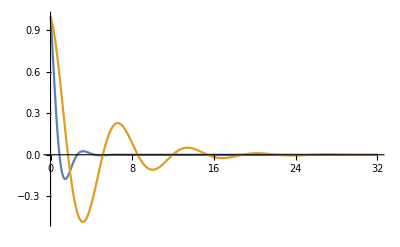

```mathematica
A={
{0.0,0,1,0},
{0,0,0,1},
{-10/3,4/3,-5/3,2/3},
{2,-2,1,-1}};
Eigenvalues[A]
Plot[{E^(-1.1 t) Cos[1.8 t],E^(-0.22t) Cos[0.92t]},{t,0, 32},PlotRange->All]
```

```mathematica
MMat=({{4, 0}, {0, 3}}); CMat=({{3, -1}, {-1, 1}}) ;KMat=({{7, -3}, {-3, 3}});
A= ArrayFlatten[({{0, IdentityMatrix[2]}, {-Inverse[MMat].KMat, -Inverse[MMat].CMat}})];
gf[t_]:=0Sin[t]
b[t_]:={4 gf[t]+2 gf'[t],0}
f[t_]:= {0,0,(4 gf[t]+2 gf'[t])/4,0}
TMax=123;
Quiet[
ySol=NDSolveValue[{
MMat.y''[t]+CMat.y'[t]+KMat.y[t]==b[t],
y[0]=={0,-1},y'[0]=={0,2}},y,{t,0, TMax}]];
zSol=NDSolveValue[{
z'[t]==A.z[t]+f[t],
z[0]=={0,-1,0,2}},z,{t,0, TMax}];
TabView[{
"y_1"->Plot[ySol[t]⟦1⟧,{t,0, TMax},PlotRange->All],
"z_1=y_1"->Plot[zSol[t]⟦1⟧,{t,0, TMax},PlotRange->All],
"y_2"->Plot[ySol[t]⟦2⟧,{t,0, TMax},PlotRange->All],
"z_2=y_2"->Plot[zSol[t]⟦2⟧,{t,0, TMax},PlotRange->All]
}]
```

1234

```mathematica
M={{1,-3},{3,1}};
Eigensystem[M]
```

{{1+3 ⅈ,1-3 ⅈ},{{ⅈ,1},{-ⅈ,1}}}